#### setup

```mathematica
options=Sequence[VertexSize->Large,VertexLabels->Placed[Automatic,{1/2,1/2}],ImageSize->Large]
```

Sequence[VertexSize→Large,VertexLabels→Placed[Automatic,{1/2,1/2}],ImageSize→Large]

## Tang Anke

# depth first search (DFS)

## basic DFS algorithm

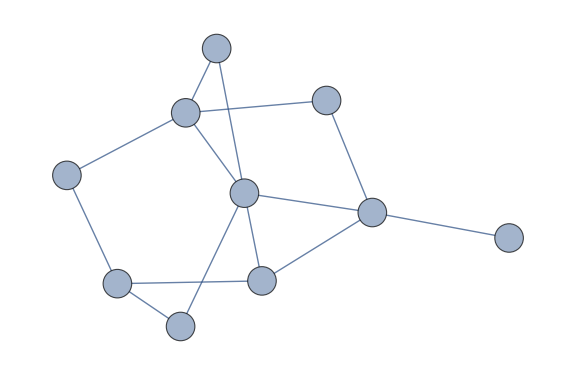

```mathematica
g=RandomGraph[{10,14},options]
```

```mathematica
ListAnimate[
Module[{visit=Function[#->LightRed],visited=Function[#->LightGray]},
GraphPlot[-Graphics-,VertexStyle->#,options]&/@FoldList[Append,{},Join[visit/@{5,6,8,7,10},visited/@{10},visit/@{2,1,4},visited/@{4},visit/@{3,9},visited/@{9,3,1,2,7,8,6,5}]]
]
]
```

-Graphics-

## applications

### connected components

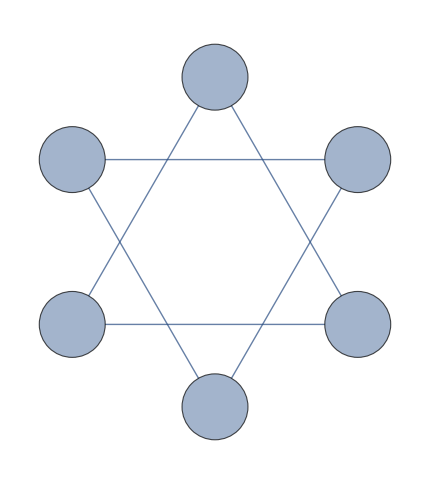

```mathematica
Graph[-Graphics-,options,GraphLayout->{"CircularEmbedding","OptimalOrder"->False}]
```

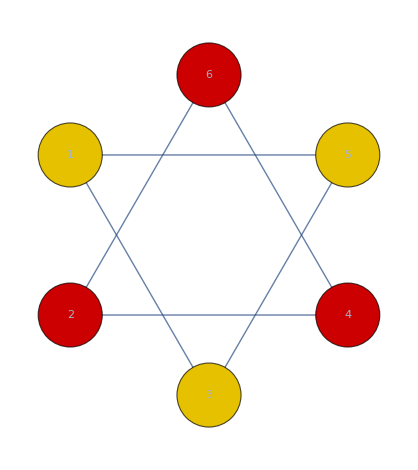

```mathematica
HighlightGraph[-Graphics-,ConnectedComponents[-Graphics-]]
```

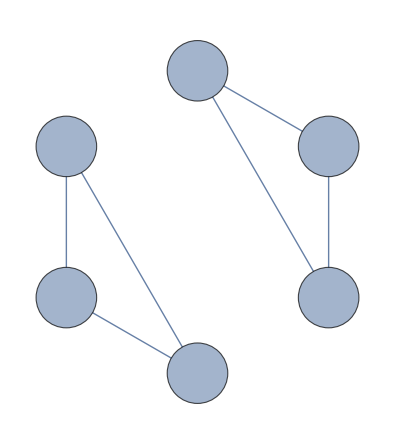

```mathematica
Graph[-Graphics-,options,GraphLayout->{"CircularEmbedding","OptimalOrder"->True}]
```

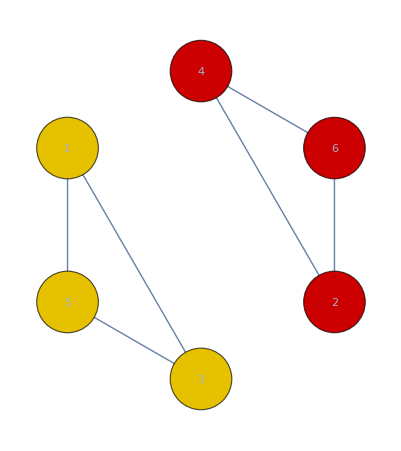

```mathematica
HighlightGraph[-Graphics-,ConnectedComponents[-Graphics-]]
```

-Graphics-

-Graphics-

-Graphics-

### topological sort

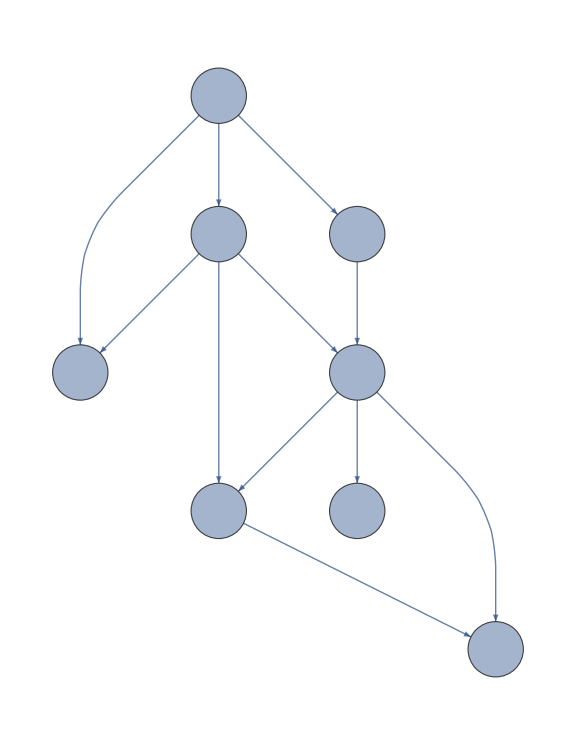

```mathematica
Graph[Range[8],{1->2,1->3,2->4,3->4,3->5,4->5,1->7,3->7,4->8,4->6,5->6},options,GraphLayout->"LayeredDigraphEmbedding"]
```

```mathematica
ListAnimate[
Module[{visit=Function[#->LightRed],visited=Function[#->LightGray]},
GraphPlot[-Graphics-,VertexStyle->#,options]&/@FoldList[Append,{},Join[visit/@{4,5,6},visited/@{6,5},visit/@{8},visited/@{8,4},visit/@{3,7},visited/@{7,3},visit/@{1,2},visited/@{2,1}]]
]
]
```

{6,5,8,4,7,3,2,1}

-Graphics-

-Graphics-

#### find bridges and articulation points

-Graphics-

-Graphics-

#### Tarjan’s algorithm for finding strongly connected components

-Graphics-

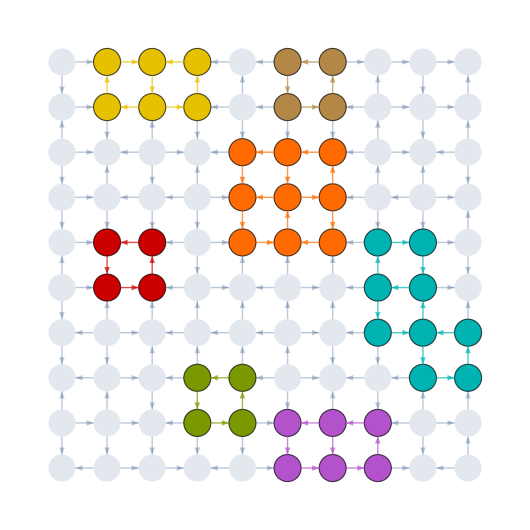

```mathematica
g=DirectedGraph[GridGraph[{10,10}],"Random",VertexSize->0.6,GraphHighlightStyle->"DehighlightFade"];
HighlightGraph[g,Select[ConnectedGraphComponents[g],VertexCount[#]>1&]]
```

#### find Eulerian path (directed graph)

```mathematica
FindSpanningTree
```

### ...

-Graphics-

# breadth first search (BFS)

## algorithm

```mathematica
ListAnimate[
Module[{visit=Function[#->LightRed],visited=Function[#->LightGray]},
GraphPlot[-Graphics-,VertexStyle->#,options]&/@FoldList[Append,{},Join[visit/@{5,6,9},visited/@{5},visit/@{4,8,1},visited/@{6},visit/@{2,3},visited/@{9,4},visit/@{7},visited/@{8,1,2,3},visit/@{10},visited/@{7,10}]]
]
]
```

-Graphics-

-Graphics-

-Graphics-

## applications

### shortest path problem (unweighted graph)

O(V+E)

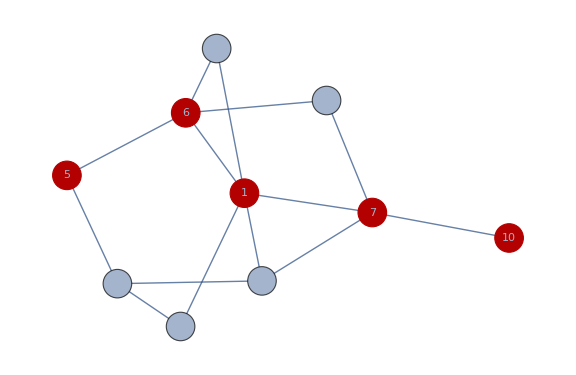

```mathematica
HighlightGraph[g,FindShortestPath[g,5,10]]
```

### single source shortest path (SSSP) on directed acyclic graph (DAG)

{-8,-7,6,-6,-10,-3,3,-8,-6,-10,-6}

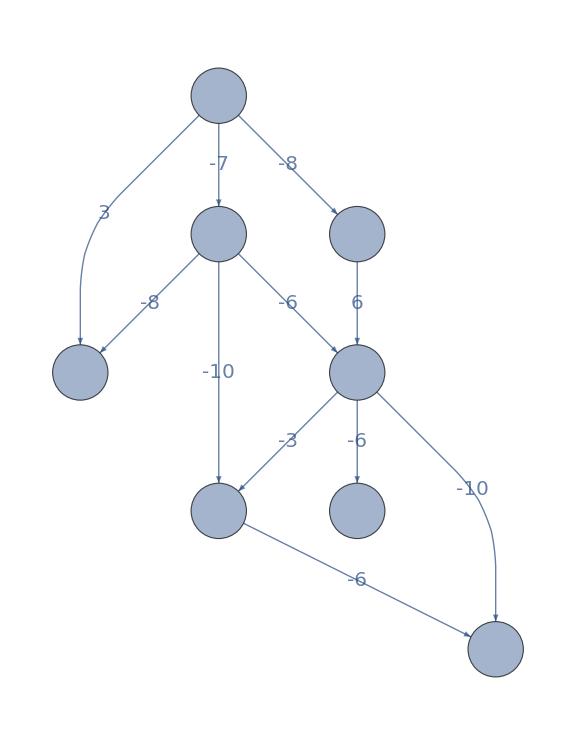

```mathematica
Module[{weights=RandomInteger[{-10,10},11],edges={1->2,1->3,2->4,3->4,3->5,4->5,1->7,3->7,4->8,4->6,5->6}},
Echo[weights];
Graph[Range[7],edges,EdgeWeight->weights,options,EdgeLabels->Thread[Rule[edges,weights]],EdgeLabelStyle->Directive[20]]
]
```

```mathematica
ListAnimate[Column[#,Alignment->Center]&/@(Thread@{
Module[{visit=Function[#->LightRed],visited=Function[#->LightGray]},
GraphPlot[-Graphics-,VertexStyle->#,options]&/@FoldList[Append,{},Join[visit/@{1,2,3,7},visited/@{1},visit/@{4},visited/@{2},visit/@{4,5,7},visited/@{3,7},visit/@{6,8,5},visited/@{4},visit/@{6},visited/@{5,8,6}]]
],
Module[
{dist=ConstantArray[Infinity,8],grid,from=ConstantArray["null",8]},grid:=Grid[{Join[{"from"},from],Join[{"distance"},dist],Join[{"vertex"},Range[8]]},Frame->All];
{
grid,
from[[1]]=1;dist[[1]]=0;grid,
from[[2]]=1;dist[[2]]=-8;grid,
from[[3]]=1;dist[[3]]=-7;grid,
from[[7]]=1;dist[[7]]=3;grid,
grid,
from[[4]]=2;dist[[4]]=-2;grid,
grid(*visted 2*),
from[[4]]=3;dist[[4]]=-13;grid,
from[[5]]=3;dist[[5]]=-17;grid,
from[[7]]=3;dist[[7]]=-15;grid,
grid,
grid(*visited 7*),
from[[6]]=4;dist[[6]]=-23;grid,
from[[8]]=4;dist[[8]]=-19;grid,
grid(*visit 5*),
grid,
grid,
grid,
grid,
grid
}
]
})]
```

#### longest path on DAG

#### Dijkstra algorithm

O((V+E)logV)

#### Bellman - Ford Algorithm

O(EV)

-Graphics-

-Graphics-

#### Floyd-Warshall algorithm (all pairs shortest path (APSP))

O(V^3)

#### ...